# Лабораторная работа №4

## Глёза Егор, группа 221701, вариант 1

## 1. Отделите графически корни алгебраического уравнения с помощью функции Plot. Найдите один из них (нецелый) с точностью ε = 10^-3 методом хорд. Укажите потребовавшееся число итераций. Проиллюстрируйте графически нахождение первых двух приближений (постройте график функции и хорды)

## Отделим графически корни уравнения

Введем функцию :

```mathematica
f[x_]:=15 x^3-86 x^2+111x-28;
```

Построим график функции :

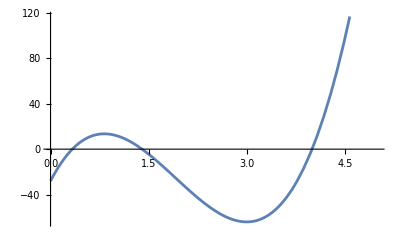

```mathematica
Plot[f[x],{x, 0 ,5},AxesOrigin->{0,0}]
```

По графику видно, что уравнение имеет три действительных корня. Они расположены в интервалах (0, 1), (1, 2) и (3, 5).

## Найдём корень на интервале (0, 1) с точностью ε = 10^-3 методом хорд.

Введем концы отрезка и точность.

```mathematica
a=0;
b=1;
e=10^-3;
```

### Метод хорд

```mathematica
Clear[x];
x[0]=b;
x1=0;
Do[
x[n+1]=a-f[a]/(f[x[n]]-f[a])(x[n]-a);
If[(x[n+1]-x[n])^2/Abs[x[n+1]+x[n-1]-2x[n]]<e,
Print["Решение x=",x[n+1]//N," получено на ", n+1, " шаге."];
x1=x[n+1];
Break[];
]
,{n,0,100}];
```

Решение x=0.333768 получено на 7 шаге.

## Проиллюстрируем графически нахождение первых двух приближений

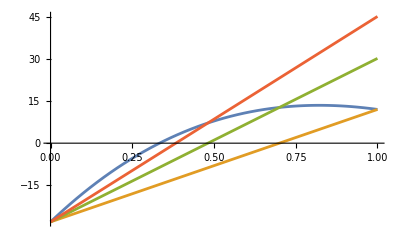

```mathematica
l[x_,x0_,x1_]:=((x-x0)(f[x1]-f[x0]))/(x1-x0)+f[x0];
Plot[{f[z],l[z,a, b],l[z,a,x[1]],l[z,a,x[2]]},{z,a,b}]
```

## 2. Отделите графически и найдите с помощью функций Solve, NSolve, Roots, FindRoot корни алгебраического уравнения . Разложите многочлен на множители, используя функцию Factor.

## Отделим графически корни уравнения

Введём функцию :

```mathematica
f[x_]:= x^6+6 x^5+12 x^4+6 x^3-9 x^2-12x-4;
```

Построим график:

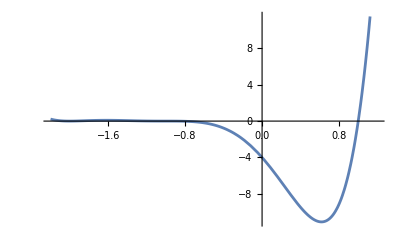

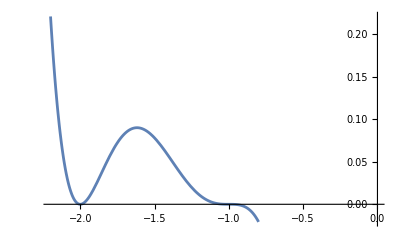

```mathematica
Plot[f[x],{x,-2.2,1.2}, AxesOrigin->{0,0}]
Plot[f[x],{x,-2.2,-0.8}, AxesOrigin->{0,0}]
```

По графику видно, что уравнение имеет три действительных корня. Они расположены в интервалах (-3, -1.7), (-1.5, 0) и (0, 2).

## Найдём корни уравнения

```mathematica
Solve[f[x]==0,x]
```

{{x→-2},{x→-2},{x→-1},{x→-1},{x→-1},{x→1}}

```mathematica
NSolve[f[x]==0,x]
```

{{x→-2.},{x→-2.},{x→-1.},{x→-1.},{x→-1.},{x→1.}}

```mathematica
Roots[f[x]==0,x]
```

x==-2||x==-2||x==-1||x==-1||x==-1||x==1

```mathematica
FindRoot[f[x],{x,-3,-1.7}]
FindRoot[f[x],{x,-1.7,0}]
FindRoot[f[x],{x,0,2}]
```

{x→-2.}

{x→-1.}

{x→1.}

Как видно, данное уравнение имеет три корня: двукратный  , трёхкратный  и .

### Разложим многочлен на множители

```mathematica
Factor[f[x]]
```

(-1+x) (1+x)^3 (2+x)^2

## 3. Отделите графически корни трансцендентного уравнения с помощью функции Plot. Найдите один из них с точностью ε = 10^-3: а) методом Ньютона; б) методом секущих. Укажите потребовавшееся число итераций.

## Отделим графически корни трансцендентного уравнения

Введем две функции  и  и построим их
графики в одной системе координат.

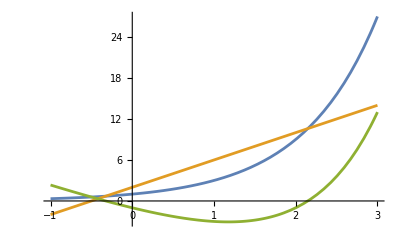

```mathematica
f[x_]=3^x;
g[x_]=4x+2;
Plot[{f[x],g[x], f[x]-g[x]},{x,-1,3}]
```

По графику видно, что уравнение имеет два действительных корня. Они расположены в интервалах (-1, 0) и (2, 3).

## Найдём корень на интервале (-1, 0) с точностью ε = 10^-3 с помощью метода Ньютона и метода секущих

Введём функцию , концы отрезка и точность:

```mathematica
h[x_]:=f[x]-g[x];
a=-1;
b=0;
e=10^-3;
```

### Метод Ньютона

```mathematica
Clear[x];
x[0]=b;
Do[
x[n+1]=x-h[x]/D[h[x],x]/.x->x[n];
If[Abs[x[n+1]-x[n]] < e,
Print["Решение x=",x[n+1]//N," получено на ", n+1, " шаге."];
Break[];
]
,{n,0,100}];
```

Решение x=-0.325081 получено на 3 шаге.

### Метод секущих

```mathematica
Clear[x];
x[0]=b;
x[1]=a;
Do[
x[n+1]=x[n]-(x[n]-x[n-1])/(h[x[n]]-h[x[n-1]])h[x[n]];
If[Abs[x[n+1]-x[n]] < e,
Print["Решение x=",x[n+1]//N," получено на ", n+1, " шаге."];
Break[];
]
,{n,100}];
```

Решение x=-0.325081 получено на 5 шаге.

## 4. Приведите уравнение (3.1 – 3.16) к виду, пригодному для итераций. Найдите его корни методом простых итераций с точностью ε = 10^-3. Укажите потребовавшееся число итераций

## Приведём уравнение к виду, пригодному для итераций

Для приведения к пригодному для итераций виду воспользуемся методом релаксации.

```mathematica
M =FindMaximum[{Abs[D[h[x],x]],-1<=x <=0},{x,0.1}][[1]];
lambda=2/M
fi[x_]:=Expand[x+lambda h[x]]
```

0.550389

## Найдём его корни методом простых итераций

### Первый корень

Введём функцию концы отрезка:

```mathematica
a=-1;
b=0;
```

Вычислим корень:

```mathematica
Clear[x];
x[0]=a;
Do[
x[n+1]=fi[x[n]];
If[Abs[x[n+1]-x[n]] < e,
Print["Решение x=",x[n+1]//N," получено на ", n+1, " шаге."];
Break[];
]
,{n,0,100}];
```

Решение x=-0.324661 получено на 29 шаге.

### Второй корень

```mathematica
M =FindMaximum[{Abs[D[h[x],x]],2<=x<=3},{x,2}][[1]];
lambda=2/M;
fi[x_]:=Expand[x-lambda h[x]]
```

Введём функцию концы отрезка:

```mathematica
a=2;
b=3;
```

Вычислим корень:

```mathematica
Clear[x];
x[0]=b-0.000001;
Do[
x[n+1]=fi[x[n]];
If[Abs[x[n+1]-x[n]] < e,
Print["Решение x=",x[n+1]//N," получено на ", n+1, " шаге."];
Break[];
]
,{n,0,100}];
```

Решение x=2.14799 получено на 8 шаге.

## 5. Решите уравнение (3.1 – 3.16) с помощью функций Solve, NSolve, FindRoot.

## Решим уравнение с помощью функций Solve, NSolve, FindRoot.

```mathematica
Solve[f[x]==g[x]]//N
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-0.325081},{x→2.14839}}

```mathematica
NSolve[f[x]==g[x]]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-0.325081},{x→2.14839}}

```mathematica
FindRoot[f[x]==g[x],{x,-1,0}]
```

{x→-0.325081}

```mathematica
FindRoot[f[x]==g[x],{x,2,3}]
```

{x→2.14839}

## 6. Дана система двух нелинейных уравнений f(x, y) = 0 и g(x, y) = 0. Используя средства пакета Mathematica, изобразите на одном чертеже кривые f(x, y) = 0 и g(x, y) = 0, и решите данную систему

Введём функции f(x, y) и g(x, y):

```mathematica
f[x_,y_]:=(x^2)^(1/3)+(y^2)^(1/3)-25^(1/3);
g[x_,y_]:=x^3+y^3-9x y;
```

Построим графики:

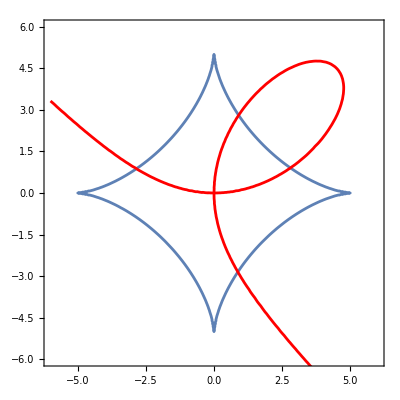

```mathematica
gr1 = ContourPlot[f[x,y]==0,{x,-6,6},{y,-6,6},Axes->True];
gr2 = ContourPlot[g[x,y]==0, {x,-6,6},{y,-10,10},Axes->True,ContourStyle->{Red}];
Show[gr1,gr2]
```

По графику видно, что кривые пересекаются в четырёх точках. Они находится вблизи точек (-3, 1), (1, 3), (3, 1) и (1, -3). Эти точки и будем использовать как начальные приближения.

```mathematica
FindRoot[{f[x,y]==0, g[x,y]==0},{x,-3},{y,1}]
```

{x→-2.8479,y→0.875031}

```mathematica
FindRoot[{f[x,y]==0, g[x,y]==0},{x,1},{y,3}]
```

{x→0.903822,y→2.80557}

```mathematica
FindRoot[{f[x,y]==0, g[x,y]==0},{x,3},{y,1}]
```

{x→2.80557,y→0.903822}

```mathematica
FindRoot[{f[x,y]==0, g[x,y]==0},{x,1},{y,-3}]
```

{x→0.875031,y→-2.8479}